## Lesson

A point at coordinates:

```mathematica
Graphics[{Point[{0,0}],Point[{2,0}]}]
```

-Graphics-

A line connecting specified coordinates:

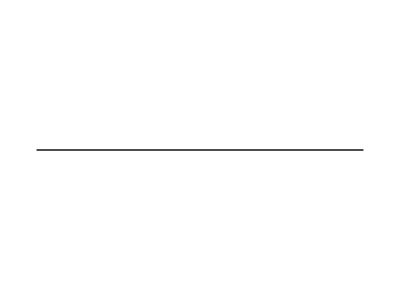

```mathematica
Graphics[Line[{{1,1},{2,1}}]]
```

A circle with center at {x, y} and radius r:



```mathematica
Graphics[Circle[{0,0},1]]
```

A regular polygon with center {x, y} and n sides each s long:

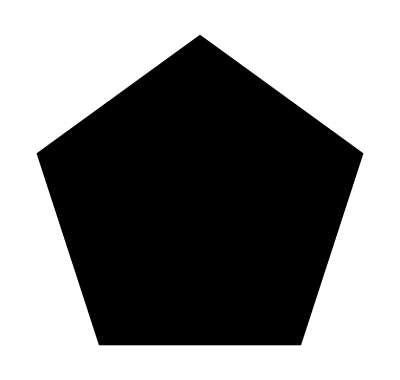

```mathematica
Graphics[RegularPolygon[{0,0},1,5]]
```

A polygon with the specified corners:

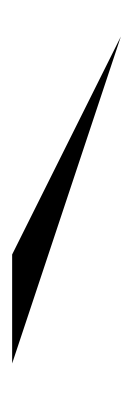

```mathematica
Graphics[Polygon[{{1,1},{2,4},{1,2}}]]
```

A sphere with center at {x, y, z} and radius r:

```mathematica
Graphics3D[Sphere[{0,1,2},1]]
```

-Graphics3D-

Specify an opacity level :

```mathematica
Graphics3D[Table[Style[Sphere[RandomInteger[10,3]],Opacity[0.5]],50]]
```

-Graphics3D-

## Questions

Q1. Make graphics of 5 concentric circles centered at {0, 0} with radii 1, 2, ... , 5.

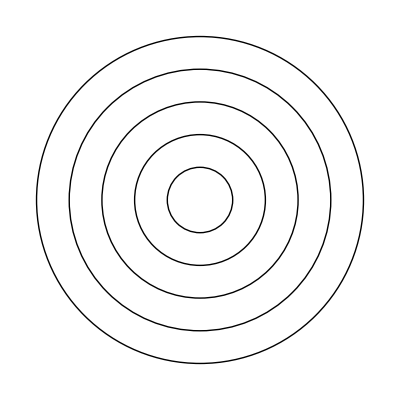

```mathematica
Graphics[Circle[{0,0},#]&/@Range[5]]
```

Q2. Make 10 concentric circles with random colours.

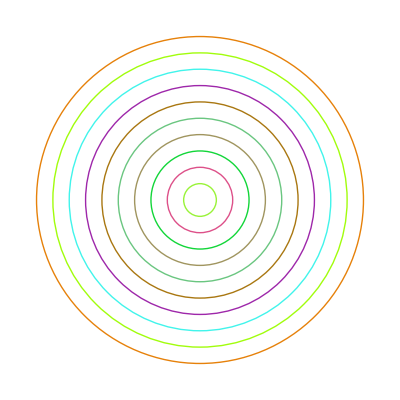

```mathematica
Graphics[Style[Circle[{0,0},#],RandomColor[]]&/@Range[10]]
```

Q3. Make graphics of a 10×10 grid of circles with radius 1 centered at integer points {x, y}.

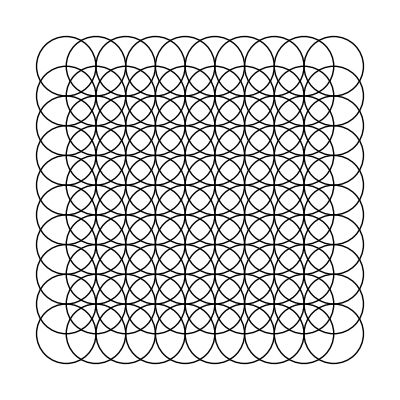

```mathematica
Graphics[Table[Circle[{i,j}],{i,10},{j,10}]]
```

Q4. Make a 10×10 grid of points with coordinates at integer positions up to 10.

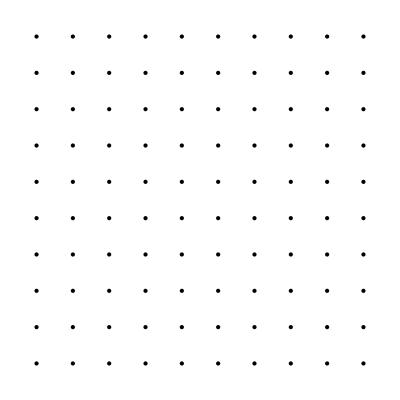

```mathematica
Graphics[Table[Point[{i,j}],{i,10},{j,10}]]
```

Q5. Make a Manipulate with between 1 and 20 concentric circles.

```mathematica
Manipulate[Graphics[Circle[{0,0},#]&/@Range[n]],{n,1,20,1}]
```

Q6. Place 50 spheres with random colours at random integer coordinates up to 10.

```mathematica
Graphics3D[Table[Style[Sphere[RandomInteger[10,3]],RandomColor[]],50]]
```

-Graphics3D-

Q7. Make a 10×10×10 array of spheres with RGB components ranging from 0 to 1. The spheres should be centered at integer coordinates, and should just touch each other.

```mathematica
Graphics3D[Table[Style[Sphere[{i,j,k},0.5],RGBColor[i/10,j/10,k/10]],{i,10},{j,10},{k,10}]]
```

-Graphics3D-

Q8. Make a Manipulate with t varying between −2 and +2 that contains circles of radius x centered at {t*x, 0} with x going from 1 to 10.

```mathematica
Manipulate[Graphics[Table[Circle[{t x,0}],{x,10}]],{t,-2,2}]
```

Q9. Make a 5×5 array of regular hexagons with size 1/2, centered at integer points.

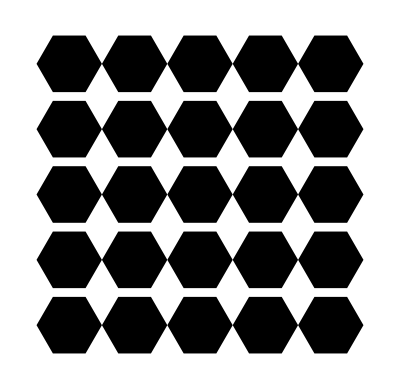

```mathematica
Graphics[Table[RegularPolygon[{i,j},1/2,6],{i,5},{j,5}]]
```

Q10. Make a line in 3D that goes through 50 random points with integer coordinates randomly chosen up to 50.

```mathematica
Graphics3D[Line[Table[RandomInteger[50,3],50]]]
```

-Graphics3D-

## Extended Questions

+Q1. Make a Manipulate to create an n×n regular grid of points at integer positions, with n going from 5 to 20.

```mathematica
Manipulate[Graphics[Table[Point[{i,j}],{i,n},{j,n}]],{n,5,20}]
```

+Q2. Place 30 radius-1 circles with random colours at random integer coordinates up to 10.

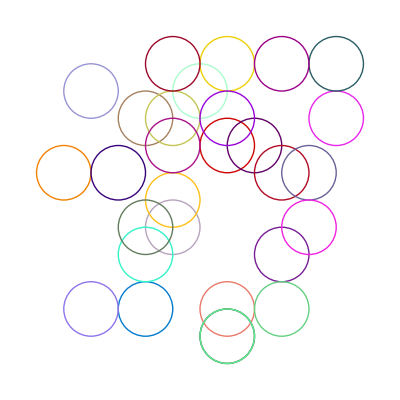

```mathematica
Graphics[Table[Style[Circle[RandomInteger[10,2]],RandomColor[]],30]]
```

+Q3. Display 100 polygons with side length 10, opacity .5, and random choices of colours, sides between 3 and 8, and integer coordinates up to 100.

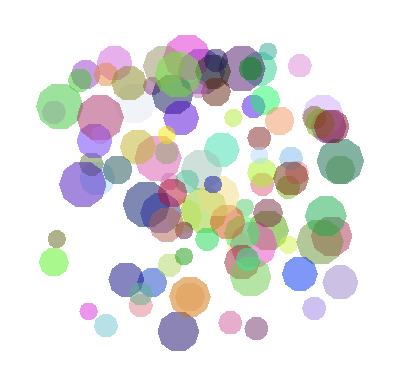

```mathematica
Graphics[Table[Style[RegularPolygon[RandomInteger[100,2],RandomInteger[{3,8}],10],RandomColor[],Opacity[0.5]],100]]
```

+Q4. Make a 10×10×10 array of points in 3D, with each point having a random colour.

```mathematica
Graphics3D[Table[Style[Point[{i,j,k}],RandomColor[]],{i,10},{j,10},{k,10}]]
```

-Graphics3D-

+Q5. Take the first two digits of numbers from 10 to 100 and draw a line that uses them as coordinates.

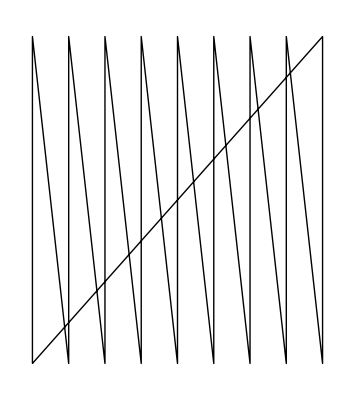

```mathematica
Graphics[Line[Take[IntegerDigits[#],2]&/@Range[10,100]]]
```

+Q6. Take the first 3 digits of numbers from 100 to 1000 and draw a line in 3D that uses them as coordinates.

```mathematica
Graphics3D[Line[Take[IntegerDigits[#],3]&/@Range[100,1000]]]
```

-Graphics3D-